## Maximization of multivariable functions: The graphical story

General instructions: 

1. To evaluate Mathematica code, get the cursor in the cell containing the code and his Shift+Enter.

2. Each occurrence of  ## corresponds to a problem. The problems are rewritten at the end of the notebook in a section entitled: Problems.  That section should be copied into a new Mathematica notebook. Your answers will be put in the new notebook.

3. Do not write Mathematica code and text in the same cell. In the cells where you are writing text, you need to format the cell for text. You can use the Format/Style/Text from the bar above, or Alt+7 to format it for text. You don’t need to format it for code.

4. This will be due on Friday, April 8. Please put a .pdf copy of your solutions on Canvas.

## Level Sets

In the first technology assignment, we wrote a module called levelset. We will make use of it in this technology assignment. It will help us understand graphically the theory behind Lagrange’s method of maximaization. Here is that module. Be sure to evaluate it.

```mathematica
levelset[e_,k_]:=Module[{k1,set1},k1=k;set1=ContourPlot[e==k1,{x,-8,8},{y,-8,8},Axes->True];Return[set1]]
```

Let’s start by plugging the expression 3 x^2 y+2x y^3 in for e and the constant 10 in for k, not forgetting that we need to leave a space between the x and the y^2. 

[Evaluate this.]

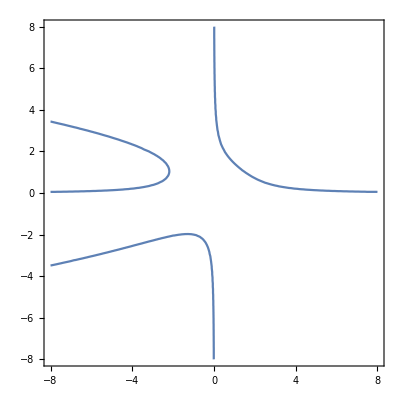

```mathematica
levelset[3 x^2 y+2x y^3,10]
```

What’s the point of this picture? It will be important to understand level sets in what follows, so let’s review a little.

The short answer is that the level set is the solutions to (f(x,y)=k)^, so that what we are looking at is a graph of the equation: 3 x^2 y+2x y^3=10

While this is accurate, if we drill down deeper, we can gain some insight into this picture as it relates to the function f(x,y)=3 x^2 y+2x y^3. First of all, notice that the domain for this function is the plane. That is to say, the function f takes points in the plane and assigns real numbers to them. It is points in the plane that we are plugging in and real numbers we are getting out. So, the first important thing to know about level sets is that they are subsets of the domain. So, we can plug the points on the level set into the function, as well as the other points in the plane not on the level set. 

This brings us to the second important fact about our level set. Not only can we plug the points from the level set into our function; but when we do, we always get the same answer out. In this case it is 10. 

To sum up: the level set of f(x,y)=3 x^2 y+2x y^3 corresponding to the level k=10 which is pictured above is the set of all the points in the plane that we can plug into the function to get out a 10.

## 1. To see if you are following the discussion, answer the following two questions: 
How many points whose x coordinate is -6 can we plug into the function f(x,y)=3 x^2 y+2x y^3 to get an answer of 10? Explain.
Why is it that no points in the output of levelset[3 x^2 y+2x y^3,10] are in the fourth quadrant?


Now, for the cases we will be looking at, level sets will be sets of 1-dimensional curves in the plane. So, we can think of the level set as dividing the plane into regions. In the example above, we saw the level set of level set of f(x,y)=3 x^2 y+2x y^3 corresponding to the level k=10 divides the plane into 4 regions. Anyone who has taken calculus for this long probably will not be surprised that with a continuous function, since we have collected all of the points where the output is k on the level set, then if there is a pair of points (x_1,y_1) and (x_2,y_2) so that  f(x_1,y_1)<k and f(x_2,y_2)>k, then (x_1,y_1) and (x_2,y_2) must be in different regions. This is essentially due to the Intermediate Value Theorem. What is more interesting is that, in most cases, if two regions are adjacent over a component of the level set, then on one side we get values smaller than k and on the other side, we get values larger than k. 

Understanding this is the key to understanding Lagrange’s method. So, I will repeat it:.

#### Key level set observation: In most cases, if two regions are adjacent over a component of the level set of f(x,y) corresponding to the level k, then on one side we get values smaller than k and on the other side, we get values larger than k.

That is to say: generally, plugging points from one side of the level set gives you a number less that k; plugging points from the other side give values higher than k. (Take note of the word “generally”. It is a weasel-word for mathematicians. It means that there are cases when the statement that follows is false, but it is true in enough of the cases that we’ll agree to be surprised when it doesn’t hold.)

So, let’s see this general statement happening in our specific case. Here again is our level set. It divides the plane into four regions:

```mathematica
levelset[3 x^2 y+2x y^3,10]
```

-Graphics-

Let’s choose a point in each of the four regions: Q=(-6,2), R=(1,-4), S=(4,5), and T=(-2,-5)

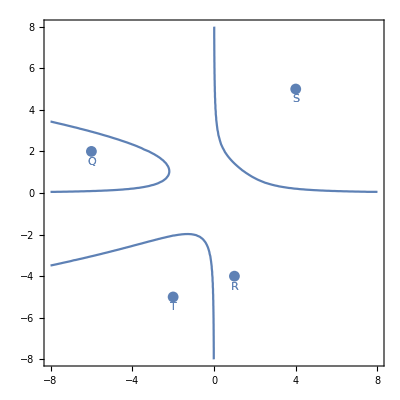

```mathematica
Show[levelset[3 x^2 y+2x y^3,10],ListPlot[{{-6,2},{1,-4},{4,5},{-2,-5}}],ListPlot[{{-6,1.5}},PlotMarkers->{"Q"}],ListPlot[{{1,-4.5}},PlotMarkers->{"R"}],ListPlot[{{4,4.5}},PlotMarkers->{"S"}],ListPlot[{{-2,-5.5}},PlotMarkers->{"T"}]]
```

Here we used the Mathematica command Show again. If you look at the list of things that we are Show-ing, the first is the familiar levelset module we wrote above; the second is a ListPlot of four points, the four dots in the picture; the last Four ListPlot’s with PlotMarkers are being used to put the labels for those points in our picture .5 below the points.

Since none of these points are on the level set, when we plug them into our function, we won’t get an answer of 10. Let’s make sure. We can plug in the points by hand; but hey, we’re sitting at a computer:

```mathematica
f[x_,y_]:=3 x^2 y+2x y^3;
f[-6,2]
f[1,-4]
f[4,5]
f[-2,-5]
```

120

-140

1240

440

As predicted, none of the outputs are 10. More importantly, what we care about these numbers is that: if we plug in any point from the big region in the middle of the picture (the region containing R, we get something less than 10; and, if we plug in any point from the other regions, which are all across a component of the level set from the big region, get something greater than 10.This is indicative of the key observation above: - when we plug in points from either side of a component of the level set of f(x,y) corresponding to k, on one side we get out a number less than k and on the other side something greater than k.

##2 Now, you should go over this with a level set for a different function. How about looking at the level sets for f(x,y)=x^2 y^2 for a positive number k? The level set should have 5 different regions. Is it the case that if one component of the level set separates two points, then plugging one in point in gives a number greater than the level and plugging in the other gives a number less than the level? Pick some points to test this. Use a picture as above to show the relationship of the points you picked to the level set.

## Max/min values: what’s going on graphically?

Here is the setting of the questions we will be asking:

	We will be given a function f:ℝ^2→ℝ and a one dimensional set C (usually described by an equation C(x,y)=c, called the constraint equation). And our question will be:
	what is the maximum and/or minimum outputs we get by plugging the points from C into the function f? 

For the time being we will ask a slightly different, but related, question:

	Given a function f:ℝ^2→ℝ and a one dimensional set C and a number k, is k either the maximum or minimum value we get out by plugging points of C into f?

At first blush, this looks like a pretty stupid question. Why? Because the answer in every case except for two, will be. “No!”. The only way the answer to this question could ever be, “Yes” is if we happened to choose as k the maximum or minimum value. But the reason we will ask this seemingly stupid question is because we can look at the level set of f corresponding to the level k and use the picture to answer the question.

Let’s look at a simple example:

Let f(x,y)=3x-4y-6.  Which of the points on the circle x^2+y^2=25, gives us the largest output?

Or, to ask it in our seemingly stupid way:
	Is k=8 either the maximum or the minimum value we would get out by plugging points of the circle x^2+y^2=25 into the function f(x,y)=3x-4y-6?
	
Let get a picture to help us answer this:

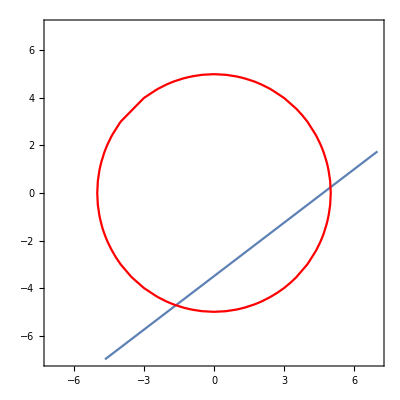

```mathematica
Show[ContourPlot[3x-4y-6==8,{x,-7,7},{y,-7,7},Axes->True],ContourPlot[x^2+y^2==25,{x,-7,7},{y,-7,7},ContourStyle->Red]]
```

In our picture, we see that the level set for the function f(x,y)=3x-4y-6 with k=8 is a blue line; and, the constraint curve, the circle, is red (the ContourStyle->Red command put into the ContourPlot command made the circle red). The two shapes intersect twice. The obvious thing this tells us is that there are two points on the circle which, when plugged into the circle give an answer of 8. 

But, let’s view our picture through the lens of the the Key Observation.

The level set (the line) divided the plane into two regions, say the northwest and southeast. According to the Key Observation plugging in points from one side of the line will yield answers that are less that 8; and points on the other side of the the line will give answers greater than 8. (Since f(0,0)=0 we can see that any point from the northwest will yield the lesser output; points from the southeast will yield the greater output.) 

The key part of this is that, since there are points on the circle in the southeast region, there are points to plug in from the circle to give an output greater than 8. And, since there are points on the circle in the northwest region, there are points to plug in from the circle to give an output less than 8. So, 8 is neither the maximum nor minimum value.

Therefore, the answer to the question: is 8 the maximum value? is “no!”, which was expected. But, there’s more to see: what made that happen was that there are points on our constraint curve in regions on either side of the level set. 

 Now, next we could look at the picture for k=9. In fact, here it is:

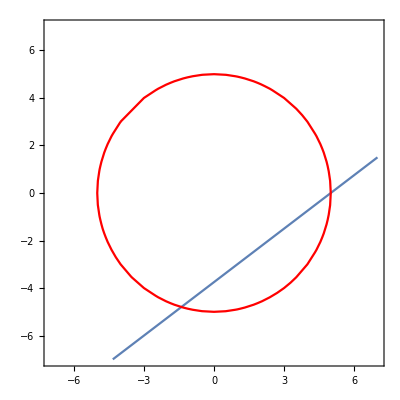

```mathematica
Show[ContourPlot[3x-4y-6==9,{x,-7,7},{y,-7,7}],ContourPlot[x^2+y^2==25,{x,-7,7},{y,-7,7},ContourStyle->Red]]
```

Again, since the constraint curve (red) crosses over the level set (blue) the answer to whether 9 is a max or min value will again be “no”. This would be too tedious to continue like this. Let’s look at a bunch of level sets at once:

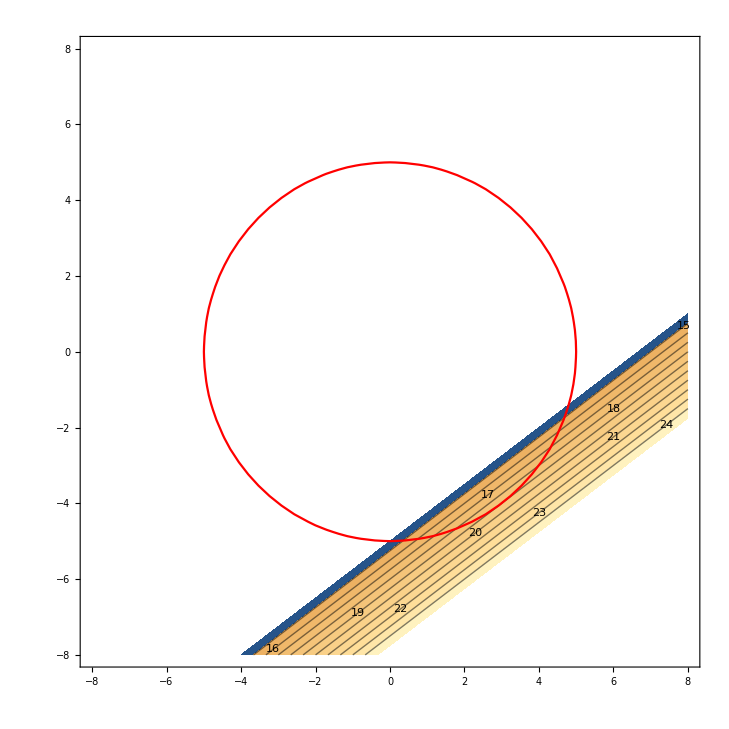

```mathematica
Show[ContourPlot[3x-4y-6,{x,-8,8},{y,-8,8},PlotRange->{14,25},Contours->10,ContourLabels->All],ContourPlot[x^2+y^2==25,{x,-8,8},{y,-8,8},ContourStyle->Red]]
```

Take a look at how the first ContourPlot command in our Show command has changed. We took away the ==’s, and added some things. Here’s a rundown on what those things did:
	PlotRange->{14,25}:  told Mathematica to make level sets with levels k where 14<k<25
	Contours->10 :           told Mathematica to plot 10 levels. 
					These two commands together implied that there would be levels plotted corresponding to the whole numbers between 14 and 25 (because there are 
					10 of them).
	ContourLabels->All:   Put the little numbers in the picture that say the level of each level set.

From this picture we see a few things (you might want to make the picture bigger by dragging a corner of it): 
	1. if k>19, the corresponding level set does not interset the circle. That is to say, for k>19, there is no point on the circle we can plug into f to get k as an output. We conclude that every point on the circle gives an answer less than or equal to 19. 
	2. if 14<k<19, the corresponding level set meets the circle twice. This means there are points to the northeast of the line which give an output smaller than k, and points southeast of the line than yield an output greater than 19. We conclude that there are two points on ths circle that yield the output k; and that k is not the max or min output. 
	3. if k=19 the corresponding level set is tangent to the circle. So, there is a point on the circle we can plug in to get the output of 19. And, every other point is to the northeast of 
the k=19 level set. Therefore, if we were to plug in another point from the circle, we would get an output less than 19.
	
	THEREFORE: the largest output of for any point on the circle is 19.

This leads us to the key graphical observation that will drive the process of finding extreme values of a function on a constraint curve:

#### Key Graphical Observation: In most cases, if the extreme value for a function f on a constraint curve C is the output k, then the level set of fcorresponding to k is tangent to C.

[Again, there is that pesky weasel-word “most”. But, it turns out that the exceptions to the Key Graphical Observation only happen with exceptions to the Key Level Set observation stated above.]

Let’s see how we can use the Key Graphical Observation to approximate extreme values in other problems.

A question: Use a picture to approximate the extreme values for f(x,y)=4 x^2+9 y^2 on the constraint curve C: xy=4

To do this, we will draw level sets for the function and the constraint curve (in red).

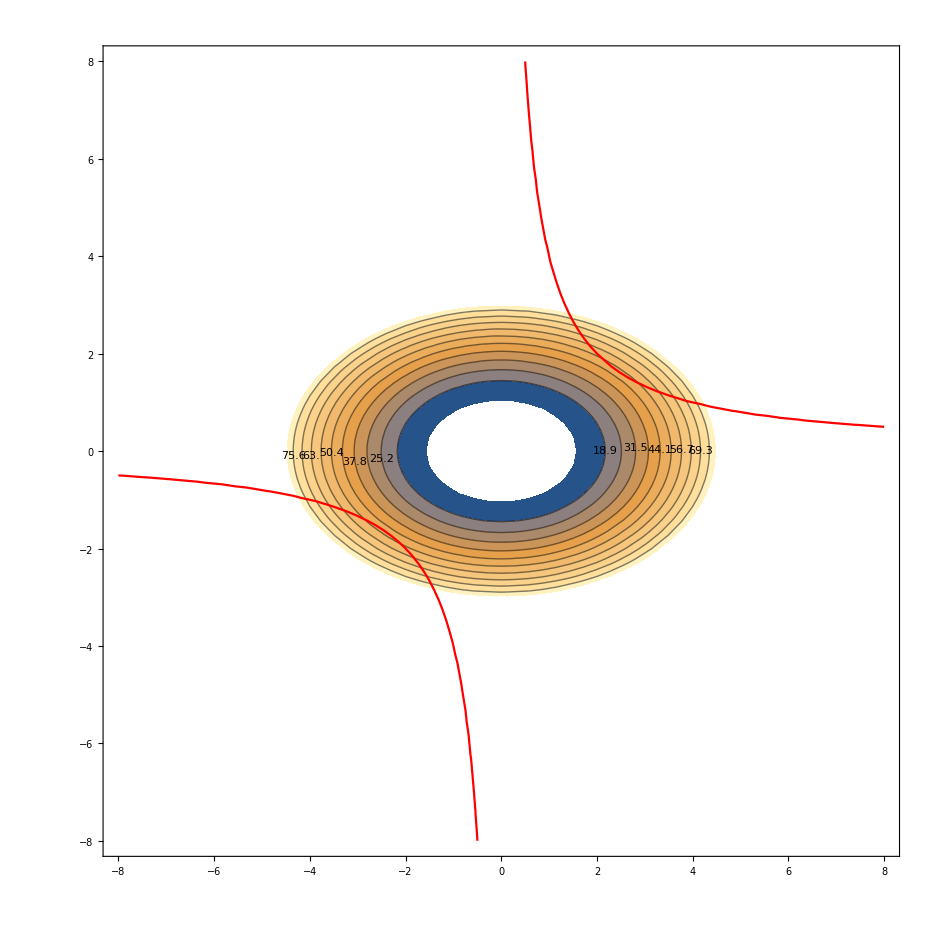

```mathematica
Show[ContourPlot[4 x^2+9 y^2,{x,-8,8},{y,-8,8},PlotRange->{10,80},Contours->10,ContourLabels->All],ContourPlot[x y==4,{x,-8,8},{y,-8,8},ContourStyle->Red]]
```

I have dragged the picture to enlargen it. We see there is a point of tangency (and therefore an extreme value) somewhere between 44.1 and 50.4. By adjusting the parameters in the ContourPlots, we can focus in on the part of the picture we are interested in.

```mathematica
Show[ContourPlot[4 x^2+9 y^2,{x,1.5,3},{y,1,3},PlotRange->{40,60},Contours->20,ContourLabels->All],ContourPlot[x y==4,{x,1.5,3},{y,1,3},ContourStyle->Red]]
```

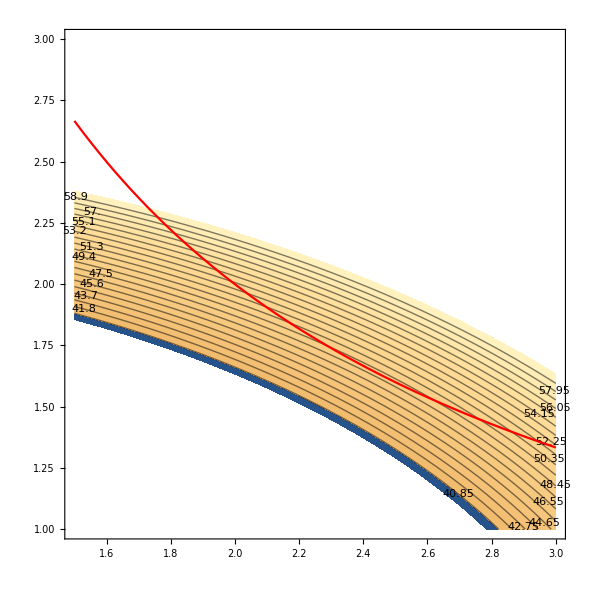

From this picture, we see that the level set which is tangent to the red constraint corresponds to some level between 47.5 and 48.45 (scrolling the mouse over the level sets gives you the values). So, we can a say that the corresponding extreme value is about 47.975 (the average of these two numbers). While this might be the wrong answer, it is certainly within 1 of the correct answer.

Now, is this a maximum value or a minimum value? Clearly, the level sets corresponding to lower levels dont’s meet the constraint curve. Therefore, this is a minimum. 

This begs the question: is there a maximum output? 

Let’s go back to the full picture and expand the PlotRange of the contour curves.

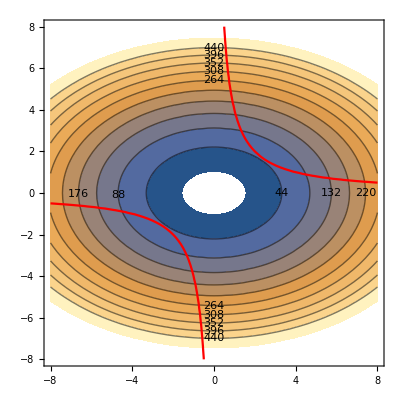

```mathematica
Show[ContourPlot[4 x^2+9 y^2,{x,-8,8},{y,-8,8},PlotRange->{10,500},Contours->10,ContourLabels->All],ContourPlot[x y==4,{x,-8,8},{y,-8,8},ContourStyle->Red]]
```

This picture suggests that no other contour will be tangent to the constraint curve. Since as k gets larger and larger, the corresponding level set always crosses the constraint curve, there will be no maximal output.

What makes this situation possible? The fact that the constraint curve wanders off to infinity. This won’t happen if the constraint curve is compact (that is, contained in a finite box and is closed.)

## Approximating the extrema using pictures

## 3. For the following, use the Show command to draw a picture combining two ContourPlots as above so that:
	1. the constraint curve  C is red; 
	2. there are enough level sets so that you can approximate the extreme values of f to within 1.
	3. What is your approximation of the maximum and minimum values?
	4. If you suspect there is either no maximum or no minimum, explain your reasoning.
	
A. 	f(x,y)=20x+30y;                    	C: x^2+y^2=4
B. 	f(x,y)=x^2 y^3                               	C: x^2+2 y^2=6
C. 	f(x,y)=(10x+100)/y                           	C:x^2+(y-8)^2=1
D.  	f(x,y)=x^2-2x+y^2+6y 		C: y=2x+1
E. 	f(x,y)=x^3-x-2y 	 		C: -6 x^2+3 y^2=6
F. 	f(x, y) = 4 x^2 - 9 y^2  		C: (x+2)^2-2y=11

## Your assignment: Problems

General instructions:
A. Copy the Your Assignment section into a new Mathematica notebook.
B. Place the answer to a question right after it. 
C. Remember to use alt+7 to format cells in which you will be typing text. You don’t need to format cells in which you will be writing Mathematica code.

To submit
D. Save the notebook as yourname_assignment 2.nb
E. Evaluate entire notebook.
F. Save as a .pdf file.
G. Submit to Canvas. This will be due on Friday, April 8.

## 1. 
A. How many points whose x coordinate is -6 can we plug into the function f(x,y)=3 x^2 y+2x y^3 to get an answer of 10? Explain.
B. Why is it that no points in the output of levelset[3 x^2 y+2x y^3,10] are in the fourth quadrant?

## 2. Look at the level sets for f(x,y)=x^2 y^2 for a specific positive number k. The level set should have 5 different regions. Is it the case that if one component of the level set separates two points, then plugging one in point in gives a number greater than the level and plugging in the other gives a number less than the level? Pick some points to test this. Use a picture to show the relationship of the points you picked to the level set.

## 3. For the following, use the Show command to draw a picture combining two ContourPlots as above so that:
	1. the constraint curve  C is red; 
	2. there are enough level sets so that you can approximate the extreme values of f to within 1.
	3. What is your approximation of the maximum and minimum values?
	4. If you suspect there is either no maximum or no minimum, explain your reasoning.
	
A. 	f(x,y)=20x+30y;                    	C: x^2+y^2=4
B. 	f(x,y)=x^2 y^3                               	C: x^2+2 y^2=6
C. 	f(x,y)=(10x+100)/y                           	C:x^2+(y-8)^2=1
D.  	f(x,y)=x^2-2x+y^2+6y 		C: y=2x+1
E. 	f(x,y)=x^3-x-2y 	 		C: -6 x^2+3 y^2=6
F. 	f(x, y) = 4 x^2 - 9 y^2  			C: (x+2)^2-2y=11
For part F, to see what you’re up against, look at the following:

```mathematica
Show[ContourPlot[4 x^2-9 y^2,{x,-10,10},{y,-10,10},PlotRange->{-500,500},Contours->30,ContourLabels->All],ContourPlot[(x+2)^2-2 y==11,{x,-10,10},{y,-10,10},ContourStyle->Red]]
```